# Get Analytical expression Lx

```mathematica
SetOptions[$FrontEnd,IgnoreSpellCheck->True]
ClearAll["Global`*"]
Needs["NumericalCalculus`"]
$Assumptions={_∈Reals,-Pi<θ<Pi &&-Pi<ϕ<Pi && -Pi<φ<Pi && -Pi<δ<Pi && c > 0 && ω >0 && w0>0 && z >0 && h >0 && E0 > 0 && r >0 && l∈Reals && x∈Reals && y ∈Reals &&t>0 && β∈Reals && α∈Reals && γ∈Reals,Tint>0}
rule2carte ={r->Sqrt[x^2+y^2],θ->ArcTan[x,y]};
rule2pol = {x->r Cos[θ],y-> r Sin[θ]};
k := ω/c
ω=1;
c=1;
zR:=1/2*k*w0^2 (*Rayleigh range*)
w[z] := w0 *Sqrt[1+(z/zR)^2] (* Beam radius *)
R[z] := z*(1+(zR/z)^2) (* Radius of curvature *)
p:=0
n := Abs[l]+2*p
G[z]:= (n+1)ArcTan[z/zR](* Gouy phase at z *)
Gpl := Sqrt[(2*Factorial[p])/(Pi*Factorial[p+Abs[l]])]*0+1
Lp := 1(* generalized Laguerre polynomials p = 0 -> Lp = 1 *)
If[p ==1,Lp = 1 +Abs[l]-(2*r^2)/w[z]^2]
f[r]=(w0*Gpl)/w[z]((r √2)/w[z])^Abs[l]*Exp[-r^2/w[z]^2]

l=1
```

{_∈ℝ,-π<θ<π&&-π<ϕ<π&&-π<φ<π&&-π<δ<π&&c>0&&ω>0&&w0>0&&z>0&&h>0&&E0>0&&r>0&&l∈ℝ&&x∈ℝ&&y∈ℝ&&t>0&&β∈ℝ&&α∈ℝ&&γ∈ℝ,Tint>0}

(2^(Abs[l]/2) ⅇ^(-r^2/(w0^2 (1+(4 z^2)/w0^4))) (r/(w0 √(1+(4 z^2)/w0^4)))^Abs[l])/(√(1+(4 z^2)/w0^4))

1

```mathematica
EzO3=Evaluate[-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](√2 ⅇ^(-1/2 ⅈ ((2 α^2)/(ⅈ+γ)+(2 β^2)/(ⅈ+γ)-2 (φ+t ω)-4 ArcTan[γ])) E0 (ⅈ-2 ⅈ α^2-2 α β+γ) ω)/(c h (-ⅈ+γ) (ⅈ+γ)^2)/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}]; (*L=1*)
EzO5=-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ]1/(c h^3 (ⅈ+γ)^5)-2 ⅈ √2 ⅇ^(-(ⅈ (2 α^2+2 β^2+(ⅈ+γ) (-2 (φ+t ω))))/(2 (ⅈ+γ))) E0 (-2 α^4+2 ⅈ α^3 β+2 ⅈ α β (-3+β^2+3 ⅈ γ)+α^2 (7-2 β^2-7 ⅈ γ)+(ⅈ+γ) (2 ⅈ-ⅈ β^2+2 γ)) ω/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}(*L=l*);
EzLGO3 = EzO3 
EzLGO5 = EzO3 +EzO5
```

-(ⅈ √2 ⅇ^(-ⅈ z-1/2 ⅈ ((2 x^2)/(w0^2 (ⅈ+(2 z)/w0^2))+(2 y^2)/(w0^2 (ⅈ+(2 z)/w0^2))-2 (t+φ)-4 ArcTan[(2 z)/w0^2])) E0 (ⅈ-(2 ⅈ x^2)/w0^2-(2 x y)/w0^2+(2 z)/w0^2))/(w0 (-ⅈ+(2 z)/w0^2) (ⅈ+(2 z)/w0^2)^2)

-(ⅈ √2 ⅇ^(-ⅈ z-1/2 ⅈ ((2 x^2)/(w0^2 (ⅈ+(2 z)/w0^2))+(2 y^2)/(w0^2 (ⅈ+(2 z)/w0^2))-2 (t+φ)-4 ArcTan[(2 z)/w0^2])) E0 (ⅈ-(2 ⅈ x^2)/w0^2-(2 x y)/w0^2+(2 z)/w0^2))/(w0 (-ⅈ+(2 z)/w0^2) (ⅈ+(2 z)/w0^2)^2)-(2 √2 ⅇ^(-ⅈ z-(ⅈ ((2 x^2)/w0^2+(2 y^2)/w0^2-2 (ⅈ+(2 z)/w0^2) (t+φ)))/(2 (ⅈ+(2 z)/w0^2))) E0 (-(2 x^4)/w0^4+(2 ⅈ x^3 y)/w0^4+(2 ⅈ x y (-3+y^2/w0^2+(6 ⅈ z)/w0^2))/w0^2+(x^2 (7-(2 y^2)/w0^2-(14 ⅈ z)/w0^2))/w0^2+(ⅈ+(2 z)/w0^2) (2 ⅈ-(ⅈ y^2)/w0^2+(4 z)/w0^2)))/(w0^3 (ⅈ+(2 z)/w0^2)^5)

```mathematica
IntEzLGO3=ComplexExpand[EzLGO3*Conjugate[EzLGO3]];
IntEzLGO3polar=IntEzLGO3/. rule2pol//Simplify;
Fθ[r_,θ_,z_]=-1/4*1/r*D[IntEzLGO3polar,θ]*Tint//Simplify;


gamma = Sqrt[1+(f[r]a0)^2+(f[r]a0)^4/4];

Lz2[r_,θ_,z_]=r*Fθ[r,θ,z]/. {E0->a0}//FullSimplify;
gLz2[r_,θ_,z_]=gamma*r*Fθ[r,θ,z]/. {E0->a0}//FullSimplify

DgLz[r_,θ_,z_] = D[gLz2[r,θ,z],r]//Simplify;
DgLz[r,-Pi/4,0]//Simplify;

rmax=Assuming[a0>0&&r>0,Simplify@Reduce[D[gLz2[r,θ,0],r]==0,r]]
rmax1 = √(1-1/(√2)) w0;
rmax1X=√(4 w0^4+8 z^2-2 √2 √(w0^8+4 w0^4 z^2+8 z^4))/(w0*2);
rmax2X=√(4 w0^4+8 z^2+2 √2 √(w0^8+4 w0^4 z^2+8 z^4))/(w0*2);
```

(2 a0^2 ⅇ^(-(4 r^2 w0^2)/(w0^4+4 z^2)) r^2 Tint w0^6 (a0^2 r^2 w0^6+ⅇ^((2 r^2 w0^2)/(w0^4+4 z^2)) (w0^4+4 z^2)^2) (2 z Cos[2 θ]+(r-w0) (r+w0) Sin[2 θ]))/((w0^4+4 z^2)^5)

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(ⅇ^((2 r^2)/w0^2) w0^2 (2 r^4-4 r^2 w0^2+w0^4)+a0^2 (4 r^6-7 r^4 w0^2+2 r^2 w0^4)) Sin[2 θ]==0,r]

```mathematica
D[Lz2[r,Pi/4,z],r]==0//Simplify
```

a0 (2 r^4 w0^2+w0^6+4 w0^2 z^2-4 r^2 (w0^4+2 z^2))==0

```mathematica
D[Lz2[r,θ,0],r]==0//Simplify
```

a0 (2 r^4-4 r^2 w0^2+w0^4) Sin[2 θ]==0

```mathematica
rmax=Assuming[a0>0&&r>0,Simplify@Reduce[D[Lz2[r,θ,0],r]==0,r]]
```

2 r==√(4-2 √2) w0||2 r==√(2 (2+√2)) w0||Sin[2 θ]==0

```mathematica
Solve[ⅇ^((2 r^2)/w0^2) w0^2 (2 r^4-4 r^2 w0^2+w0^4)==0,r]//FullSimplify
```

{{r→√(1-1/(√2)) w0},{r→√(1+1/(√2)) w0}}

```mathematica
rmax=Assuming[a0>0&&r>0,Simplify@Reduce[D[Lz2[r,θ,0],r]==0,r]]
```

2 r==√(4-2 √2) w0||2 r==√(2 (2+√2)) w0||Sin[2 θ]==0

```mathematica
LzMax =Lz2[rmax1,Pi/4,0]//Simplify
```

-((-1+√2) a0^2 ⅇ^(-2+√2) Tint)/w0^2

```mathematica
LzMax =Lz2[w0/Sqrt[2],Pi/4,0]//Simplify
```

-(a0^2 Tint)/(2 ⅇ w0^2)

```mathematica
(a0^2 Tint)/(2 ⅇ w0^2)-((-1+√2) a0^2 ⅇ^(-2+√2) Tint)/w0^2//Simplify
```

-(a0^2 (-ⅇ+2 (-1+√2) ⅇ^(√2)) Tint)/(2 ⅇ^2 w0^2)

# Numerical

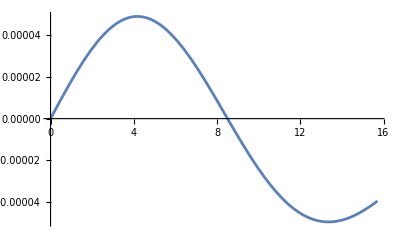

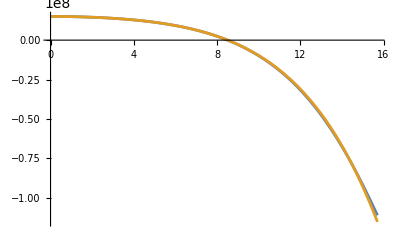

```mathematica
l0=2*Pi;
w0=2.5*l0;
Tp=12*l0;
Tint = 3/8*Tp;
a0=0.1;
z=5*l0;
Plot[{DgLz[r,-Pi/4,0]},{r,0,w0}]
Plot[{(ⅇ^((2 r^2)/w0^2) w0^2 (2 r^4-4 r^2 w0^2+w0^4)+a0^2 (4 r^6-7 r^4 w0^2+2 r^2 w0^4)),w0^6+2 (-1+a0^2) w0^4 r^2-(4+7 a0^2) w0^2 r^4+(-8/3+4 a0^2) r^6},{r,0,w0}]
```

```mathematica
Lz2[3,5,0]
```

0.0366627

```mathematica
gamma
```

√(1+0.0643368 ⅇ^(-0.00761208 r^2) r^2+0.00103481 ⅇ^(-0.0152242 r^2) r^4)

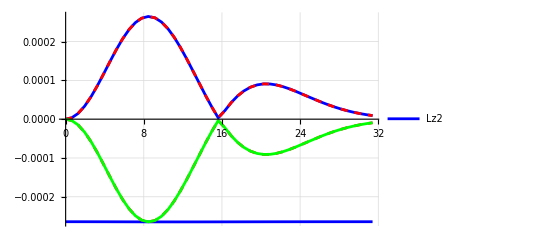

```mathematica
Plot[{gamma*Lz2[8.5,Pi/4,0],gamma*FindMaximum[Lz2[r,theta,0],{theta,0,2Pi}][[1]],gamma*FindMinimum[Lz2[r,theta,0],{theta,0,2Pi}][[1]],
	FindMaximum[gLz2[r,theta,0],{theta,0,2Pi}][[1]],FindMinimum[gLz2[r,theta,0],{theta,0,2Pi}][[1]]},
{r,0.001,2*w0},PlotStyle->{Blue,Blue,{Red,Dashed},{Red,Dashed},Green,Green,Orange,Orange},PlotLegends->Placed[{"Lz2",None},Right],GridLines->Automatic,PlotPoints->25,MaxRecursion->1]
```

```mathematica
a0=0.1
rmax1
Lz2[rmax1,Pi/4,5*l0]
```

0.1

8.63266

-0.000226906